## Min Heap Implementation

I will implement a min-Heap using a list a. The Heap will store tuples {t, i}, where t is the time of the next collision including particle i.

### HeapQ

Tests if a is a min-Heap in O(N).

#### Definition

```mathematica
HeapQ[a_List]:=Module[{n=a//Length},
And@@Table[a⟦Floor[i/2]⟧≤ a⟦i⟧, {i, 2, n}]
]
```

#### Testing

```mathematica
a=Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
HeapQ[a]
```

True

### HSwap

#### Definition

Function swaps elements i and j of list a. Argument a has to be in variable (unevaluated) form

```mathematica
HSwap=Function[{a, i, j},
{a⟦i⟧, a⟦j⟧}={a⟦j⟧, a⟦i⟧};,
HoldFirst];
```

```mathematica
HSwap2=Function[{a, i, j},
{a⟦i⟧, a⟦j⟧}={a⟦j⟧, a⟦i⟧};
a];
```

#### Testing

```mathematica
a={1,2,3}
```

{1,2,3}

```mathematica
a=HSwap2[Unevaluated@a, 1, 2]
```

{2,1,3}

```mathematica
a
```

{2,1,3}

```mathematica
x={1, 2, 3};
HSwap[x,1,3]
```

```mathematica
x
```

{3,2,1}

```mathematica
Clear[a, i, j]
```

```mathematica
a={1,2,3,4,5}
```

{1,2,3,4,5}

```mathematica
a[[1]]=a[[4]]
```

4

```mathematica
a[[1]]
```

4

```mathematica
HSwap[a, 1, 4]
```

Set::setps: {4,2,3,4,5} in the part assignment is not a symbol.

4

### HeapifyDown

Recursively updates downwards, following minHeap property.

#### Definition

```mathematica
HeapifyDown=Function[{a, i},
Module[{ n=a//Length},
Which[n<2i,
	a,
	(*at leaf*)
	n≤2i && a⟦i⟧≥ a⟦2i⟧, 
	{a⟦i⟧, a⟦2i⟧}={a⟦2i⟧, a⟦i⟧};
	HeapifyDown[a, 2i];,
	(*only left child*)
	a⟦i⟧≤ a⟦2i⟧ && a⟦i⟧≤ a⟦2i+1⟧, 
	a,
	(*property satisfied*)
	a⟦i⟧≥Min[a⟦2i⟧, a⟦2i+1⟧] && a⟦2i⟧≤  a⟦2i+1⟧,
	{a⟦i⟧, a⟦2i⟧}={a⟦2i⟧, a⟦i⟧};
	HeapifyDown[a, 2i];,
	(*swap with left child*)
	a⟦i⟧≥  Min[a⟦2i⟧, a⟦2i+1⟧] && a⟦2i⟧>a⟦2i+1⟧,
	{a⟦i⟧, a⟦2i+1⟧}={a⟦2i+1⟧, a⟦i⟧};
	HeapifyDown[a, 2i+1];
	(*swap with right child*)
 ]
],
HoldFirst
];
```

#### Testing

```mathematica
a={10,1,2,3,4}
```

{10,1,2,3,4}

```mathematica
a⟦1⟧
```

10

```mathematica
HeapifyDown[a, 1]
```

```mathematica
a//HeapQ
```

True

### HeapifyUp

Recursively updates upwards, following minHeap property

```mathematica
HeapifyUp=Function[{a, i},
Module[{ n=a//Length},
Which[
i==1,
a,
(*at root*)
a⟦i⟧≥ a⟦Floor[i/2]⟧,
a,
(*satisfies minHeap prop, return*)
a⟦i⟧≤ a⟦Floor[i/2]⟧,
{a⟦i⟧, a⟦Floor[i/2]⟧}={a⟦Floor[i/2]⟧, a⟦i⟧};
HeapifyUp[a, Floor[i/2]];
(*swap with parent, if greater*)
 ]
],
HoldFirst
];
```

#### Testing

```mathematica
a={1,2,3,4,5,6,7,1};
HeapifyUp[a, 8]
```

```mathematica
a//HeapQ
```

True

### Insert

This function appends the element to the end of the min-heap, and places it with HeapifyUp.

#### Definition

```mathematica
HInsert=Function[{H, element},
AppendTo[H, element];
HeapifyUp[H, H//Length];,
HoldFirst
];
```

#### Testing

```mathematica
h={1,2,3,4,5,6};
```

```mathematica
HInsert[h, 1]
```

```mathematica
h
```

{1,2,1,4,5,6,3}

### extractMin

#### Definition

```mathematica
extractMin=Function[{H},
Module[{last},
HSwap[H,1, H//Length];
last=H⟦-1⟧;
H=Most@H;
HeapifyDown[H, 1];
last
],
HoldFirst
];
```

### Testing

```mathematica
h=Range[100]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

```mathematica
extractMin[h]
```

1

```mathematica
h//HeapQ
```

HeapQ[{2,4,3,8,5,6,7,16,9,10,11,12,13,14,15,32,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,64,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,100,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99}]

## Scratch

```mathematica
l={1,2,3,4,5,6}
```

{1,2,3,4,5,6}

```mathematica
Most[l]
```

{1,2,3,4,5}

```mathematica
l
```

{1,2,3,4,5,6}

```mathematica
tester=Table[(extractMin[Range[10^n]]//AbsoluteTiming)⟦1⟧, {n, 3}]
```

Set::setps: Range[10^n] in the part assignment is not a symbol.

Set::write: Tag Range in Range[10] is Protected.

Set::setps: Range[10^n] in the part assignment is not a symbol.

General::stop: Further output of Set::setps will be suppressed during this calculation.

Set::write: Tag Range in Range[100] is Protected.

Set::write: Tag Range in Range[1000] is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.

{0.00354587,0.00322606,0.00220243}

```mathematica
t=Table[Range[10^i], {i, 7}];
```

```mathematica
v=Table[(extractMin[t⟦i⟧]//AbsoluteTiming)⟦1⟧, {i,7}];
```

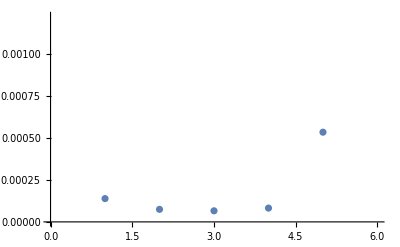

```mathematica
v//ListPlot
```

```mathematica
l=Range[10^6]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,999880,999941,999942,999943,999944,999945,999946,999947,999948,999949,999950,999951,999952,999953,999954,999955,999956,999957,999958,999959,999960,999961,999962,999963,999964,999965,999966,999967,999968,999969,999970,999971,999972,999973,999974,999975,999976,999977,999978,999979,999980,999981,999982,999983,999984,999985,999986,999987,999988,999989,999990,999991,999992,999993,999994,999995,999996,999997,999998,999999,1000000}
 |  |  |  |

```mathematica
ClearSystemCache
```

ClearSystemCache

```mathematica
l=Range[10^2];
(extractMin[l]//AbsoluteTiming)⟦1⟧
```

0.000478396

```mathematica
l=Range[10^3];
(extractMin[l]//AbsoluteTiming)⟦1⟧
```

0.000714384

```mathematica
l=Range[10^4];
(extractMin[l]//AbsoluteTiming)⟦1⟧
```

0.000626408

```mathematica
l=Range[10^5];
(extractMin[l]//AbsoluteTiming)⟦1⟧
```

0.00154997

```mathematica
l=Range[10^8];
(extractMin[l]//AbsoluteTiming)⟦1⟧
```

General::nomem: The current computation was aborted because there was insufficient memory available to complete the computation.

Throw::sysexc: Uncaught SystemException returned to top level. Can be caught with Catch[…, _SystemException].

SystemException[MemoryAllocationFailure]

```mathematica
l=RandomReal[10, 1000]//Sort;
```

```mathematica
(l//extractMin//AbsoluteTiming)⟦1⟧
```

0.000720803

```mathematica
l4=RandomReal[10, 10000]//Sort;
```

```mathematica
(l4//extractMin//AbsoluteTiming)⟦1⟧
```

0.00105987

```mathematica
l5=RandomReal[10, 100000]//Sort;
```

```mathematica
(l5//extractMin//AbsoluteTiming)⟦1⟧
```

0.000942444

```mathematica
l6=RandomReal[10, 1000000]//Sort;
```

```mathematica
(l6//extractMin//AbsoluteTiming)⟦1⟧
```

0.023048

```mathematica
l7=RandomReal[10, 10000000]//Sort;
```

```mathematica
(l7//extractMin//AbsoluteTiming)⟦1⟧
```

0.172846

```mathematica
Clear[]
```

## New Implementation - Works Bitches!!!!!!!!!

```mathematica
heap=Range[100];
```

### heapQnew

Tests if a is a min-Heap in O(N).

#### Definition

```mathematica
heapQnew[a_List]:=Module[{n=a//Length},
And@@Table[a⟦Floor[i/2]⟧≤ a⟦i⟧, {i, 2, n}]
]
```

#### Testing

```mathematica
a=Range[10];
```

```mathematica
heapQnew[a]
```

True

### heapswapnew

Swaps elements i and j of heap.

#### Definition

```mathematica
heapswapnew[i_,j_]:={heap⟦i⟧, heap⟦j⟧}={heap⟦j⟧, heap⟦i⟧};
```

#### Testing

```mathematica
heapswapnew[1, 2];
```

```mathematica
heap
```

{2,1,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

```mathematica
heapswapnew[1, 2];
```

### heapifyDownnew

#### Definition

```mathematica
heapifyDownnew=Function[{i},
Module[{ n=heap//Length},
Which[n<2i,
	heap,
	(*at leaf*)
	n≤2i && heap⟦i⟧≥ heap⟦2i⟧, 
	{heap⟦i⟧, heap⟦2i⟧}={heap⟦2i⟧, heap⟦i⟧};
	heapifyDownnew[2i];,
	(*only left child*)
	heap⟦i⟧≤ heap⟦2i⟧ && heap⟦i⟧≤ heap⟦2i+1⟧, 
	heap,
	(*property satisfied*)
	heap⟦i⟧≥Min[heap⟦2i⟧, heap⟦2i+1⟧] && heap⟦2i⟧≤  heap⟦2i+1⟧,
	{heap⟦i⟧, heap⟦2i⟧}={heap⟦2i⟧, heap⟦i⟧};
	heapifyDownnew[2i];,
	(*swap with left child*)
	heap⟦i⟧≥  Min[heap⟦2i⟧, heap⟦2i+1⟧] && heap⟦2i⟧>heap⟦2i+1⟧,
	{heap⟦i⟧, heap⟦2i+1⟧}={heap⟦2i+1⟧, heap⟦i⟧};
	heapifyDownnew[2i+1];
	(*swap with right child*)
 ]
],
HoldFirst
];
```

#### Testing

```mathematica
heap=Range[100];
```

```mathematica
heap⟦1⟧=100;
heap;
```

{100,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

```mathematica
heapifyDownnew[1]
```

```mathematica
heap//heapQnew
```

True

### heapifyUpnew

#### Definition

```mathematica
heapifyUpnew=Function[{i},
Module[{ n=heap//Length},
Which[
i==1,
heap,
(*at root*)
heap⟦i⟧≥ heap⟦Floor[i/2]⟧,
heap,
(*satisfies minHeap prop, return*)
heap⟦i⟧≤ heap⟦Floor[i/2]⟧,
{heap⟦i⟧, heap⟦Floor[i/2]⟧}={heap⟦Floor[i/2]⟧, heap⟦i⟧};
heapifyUpnew[Floor[i/2]];
(*swap with parent, if greater*)
 ]
],
HoldFirst
];
```

#### Testing

```mathematica
heap=Range[100];
heap⟦100⟧=1;
```

```mathematica
heapifyUpnew[100]
```

```mathematica
heap//heapQnew
```

True

### hInsertnew

#### Definition

```mathematica
HInsertnew=Function[{element},
AppendTo[heap, element];
heapifyUpnew[ heap//Length];,
HoldFirst
];
```

#### Testing

```mathematica
heap=Range[100];
```

```mathematica
HInsertnew[1]
```

```mathematica
heap//heapQnew
```

True

#### Definition

```mathematica
extractMin=Function[{H},
Module[{last},
HSwap[H,1, H//Length];
last=H⟦-1⟧;
H=Most@H;
HeapifyDown[H, 1];
last
],
HoldFirst
];
```